### Estimation of entries in the detector based on pseudorapidity values

Definition of η

```mathematica
η[θ_]=-Log[Tan[θ/2]]
```

-Log[Tan[θ/2]]

then easily:

```mathematica
θ[η_]=2*ArcTan[E^-η]
```

2 ArcTan[ⅇ^-η]

which can be plotted

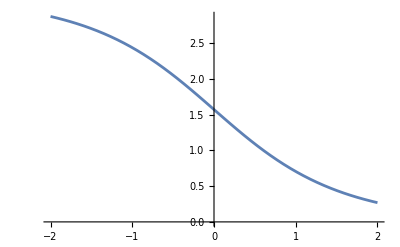

```mathematica
Plot[θ[x],{x,-2,2}]
```

And now given the geometry we have, it is easy to calculate the angular values of acceptance

```mathematica
α=θ[2]*180/π//N
```

15.4146

```mathematica
β=θ[-2]*180/π//N
```

164.585

```mathematica
β'=180-β
```

15.4146

Now from easy geometrical arguments:

```mathematica
L=27
```

27

```mathematica
r=√(4^2+(L/2)^2)//N
```

14.0801

and finally

```mathematica
α'=ArcSin[4/r]*180/π
```

16.5044